1. Sea X una variable aleatoria con distribución N(0,1) y sea Y la variable aleatoria Y=X |-1 ≤ X ≤ 1.
    a) Obtener la densidad de la v.a. Y
    b) Representar de forma conjunta la densidad de X y la densidad de la v.a. Y.
    c) Calcular P(-0.5 < Y < 0.5).

a) La función de densidad de Y viene dada por: (ⅇ^(-x^2/2))/(√(2 π) Erf[1/(√2)])

```mathematica
densidadX = PDF[NormalDistribution[0,1],x]
```

(ⅇ^(-x^2/2))/(√(2 π))

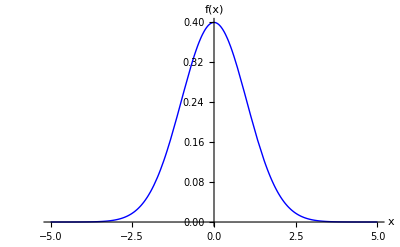

```mathematica
Plot[densidadX,{x,-5,5},PlotRange->All,PlotStyle->{Blue,Thick},AxesLabel->{"x", "f(x)"}]
```

```mathematica
densidadY = densidadX/Integrate[densidadX,{x,-1,1}]
```

(ⅇ^(-x^2/2))/(√(2 π) Erf[1/(√2)])

b) Gráficas de las funciones de densidad de X e Y

```mathematica
Plot[{densidadY, densidadX},{x,-3,3},PlotRange->All,PlotStyle->{{Blue,Thick},{Green, Thick}},AxesLabel->{"x", "f(x)"}]
```

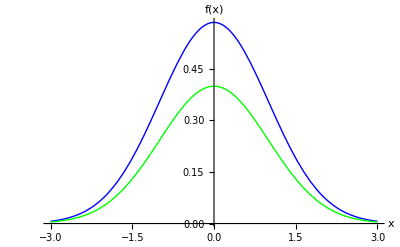

c) P (-0.5 < Y < 0.5) = 0.560906

```mathematica
N[Integrate[densidadY,{x,-0.5,0.5}]]
```

0.560906

2. Resolver el problema 4 de la relación de la distribución Normal.

El tiempo (en meses) que tarda un graduado en Matemáticas en encontrar su primer trabajo
es una v.a. X que sigue una ley normal de media 6 meses y tal que P (X > 9) = 0.02275.00 y dibuje la gr ́afica de la funci ́on de densidad indicando la posici ́on de la media
y los extremos de dicha gr ́afica en donde se encuentra el 99.994% de los valores.
b) Si un graduado en Matem ́aticas lleva buscando trabajo m ́as de 5 meses, ¿cu ́al es la
probabilidad de que lo encuentre antes de que termine el 8 mes?
c) ¿Cu ́antos meses, c ́omo m ́aximo, tardan en encontrar su primer trabajo en 33% de los
graduados en Matem ́aticas?
d) Se eligen 25 graduados en Matem ́aticas al azar, ¿cu ́al es la probabilidad de que el tiempo
medio (en meses) que tardan en conseguir su primer trabajo sea un valor inferior a 6.5
meses?.00 y dibuje la gr ́afica de la funci ́on de densidad indicando la posici ́on de la media
y los extremos de dicha gr ́afica en donde se encuentra el 99.994% de los valores.
b) Si un graduado en Matem ́aticas lleva buscando trabajo m ́as de 5 meses, ¿cu ́al es la
probabilidad de que lo encuentre antes de que termine el 8 mes?
c) ¿Cu ́antos meses, c ́omo m ́aximo, tardan en encontrar su primer trabajo en 33% de los
graduados en Matem ́aticas?
d) Se eligen 25 graduados en Matem ́aticas al azar, ¿cu ́al es la probabilidad de que el tiempo
medio (en meses) que tardan en conseguir su primer trabajo sea un valor inferior a 6.5
meses?.00 y dibuje la gr ́afica de la funci ́on de densidad indicando la posici ́on de la media
y los extremos de dicha gr ́afica en donde se encuentra el 99.994% de los valores.
b) Si un graduado en Matem ́aticas lleva buscando trabajo m ́as de 5 meses, ¿cu ́al es la
probabilidad de que lo encuentre antes de que termine el 8 mes?
c) ¿Cu ́antos meses, c ́omo m ́aximo, tardan en encontrar su primer trabajo en 33% de los
graduados en Matem ́aticas?
d) Se eligen 25 graduados en Matem ́aticas al azar, ¿cu ́al es la probabilidad de que el tiempo
medio (en meses) que tardan en conseguir su primer trabajo sea un valor inferior a 6.5
meses?.00 y dibuje la gr ́afica de la funci ́on de densidad indicando la posici ́on de la media
y los extremos de dicha gr ́afica en donde se encuentra el 99.994% de los valores.
b) Si un graduado en Matem ́aticas lleva buscando trabajo m ́as de 5 meses, ¿cu ́al es la
probabilidad de que lo encuentre antes de que termine el 8 mes?
c) ¿Cu ́antos meses, c ́omo m ́aximo, tardan en encontrar su primer trabajo en 33% de los
graduados en Matem ́aticas?
d) Se eligen 25 graduados en Matem ́aticas al azar, ¿cu ́al es la probabilidad de que el tiempo
medio (en meses) que tardan en conseguir su primer trabajo sea un valor inferior a 6.5
meses?.00 y dibuje la gr ́afica de la funci ́on de densidad indicando la posici ́on de la media
y los extremos de dicha gr ́afica en donde se encuentra el 99.994% de los valores.
b) Si un graduado en Matem ́aticas lleva buscando trabajo m ́as de 5 meses, ¿cu ́al es la
probabilidad de que lo encuentre antes de que termine el 8 mes?
c) ¿Cu ́antos meses, c ́omo m ́aximo, tardan en encontrar su primer trabajo en 33% de los
graduados en Matem ́aticas?
d) Se eligen 25 graduados en Matem ́aticas al azar, ¿cu ́al es la probabilidad de que el tiempo
medio (en meses) que tardan en conseguir su primer trabajo sea un valor inferior a 6.5
meses?

a) Calcule la desviación típica y dibuje la gráfica de la función de densidad indicando la posición de la media y los extremos de dicha gráfica en donde se encuentra el 99.994 % de los valores .

```mathematica
Solve[1-CDF[NormalDistribution[6,s],9]==0.02275,s](*1-P(X9)=0.02275*)
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{s→1.5}}

La desviación típica es 1, 5.

```mathematica
densidadX = PDF[NormalDistribution[6,1.5],x]
```

0.265962 ⅇ^(-0.222222 (-6+x)^2)

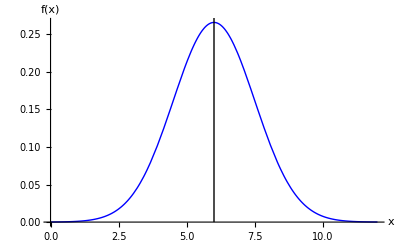

```mathematica
Plot[densidadX,{x,0,12},PlotRange->All,PlotStyle->{Blue,Thick},AxesLabel->{"x", "f(x)"},Epilog->Line[{{6,0},{6,1}}]]
```

El intervalo de confianza que se nos pide como extremo de la gráfica es , es decir [0,12].

```mathematica
NIntegrate[densidadX,{x,0,12}]
```

0.999937

b) Si un graduado en Matemáticas lleva buscando trabajo más de 5 meses, cual es la
probabilidad de que lo encuentre antes de que termine el 8 mes?

```mathematica
NIntegrate[densidadX,{x,5,8}]/NIntegrate[densidadX,{x,5,Infinity}](*P(X<=8 | x>5)=P(5<x<8)/P(x>5)*)
```

0.87798

La probabilidad será de 0.87798

c) ¿Cuántos meses, cómo máximo, tardan en encontrar su primer trabajo en 33 % de los
graduados en Matemáticas?

```mathematica
NSolve[CDF[NormalDistribution[6,1.5],t]==0.33,t]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

```mathematica
Solve[CDF[NormalDistribution[6,1.5],t]==0.33]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{t→5.34013}}

El percentil 33 es : 5.34013

d) Se eligen 25 graduados en Matemáticas al azar, cuál es la probabilidad de que el tiempo
medio (en meses) que tardan en conseguir su primer trabajo sea un valor inferior a 6.5
meses?.00 y dibuje la gr ́afica de la funci ́on de densidad indicando la posici ́on de la media
y los extremos de dicha gr ́afica en donde se encuentra el 99.994% de los valores.

Para calcular la probabilidad respecto a una muestra consideramos la distribución normal con la misma media y la siguiente desviación típica: , luego la probabilidad buscada es: 0.95221

```mathematica
CDF[NormalDistribution[6,0.3],6.5]
```

0.95221

3. Aproximación de una distribución Binomial por una distribución de Poisson

La distribución de Poisson surgió como una convergencia de la distribución Binomial de parámetros n y p,  Bi(n,p), con las siguientes condiciones: 
            n->∞,  p->0 y además np->λ, con λ constante. 

En tales condiciones la distribución Binomial se puede aproximar por una distribución de Poisson de parámetro λ=np, Po(λ) (Teorema de Poisson, 1832)

Obsérvese que la media de la distribución Bi(n,p) es np que coincide con la media de la distribución Po(λ=np); sin embargo la varianza de la distribución Bi(n,p) es npq y la de la distribución de Po(λ=np) es np. Por lo tanto esta aproximación será más exacta cuanto más próximo a 1 sea q y por lo tanto cuanto más próximo a cero sea p.

Problema: Supóngase que en una gran población la proporción de personas que tiene cierta enfermedad es del 1%. Determinar la probabilidad de que en un grupo aleatorio de 200 personas al menos 4 tengan la enfermedad.
Obtener esta probabilidad de forma directa mediante una distribución binomial y mediante la aproximación por una distribución de Poisson.
Representar gráficamente de forma simultánea las gráficas de las dos distribuciones del problema

```mathematica
binomial = PDF[BinomialDistribution[200,0.01]]
```

Function[x,Piecewise[{{0.01^x 0.99^(200-x) Binomial[200,x], 0≤x≤200}, {0, True}}],Listable]

```mathematica
binomial[4]
```

0.0902197

```mathematica
poison = PDF[PoissonDistribution[2]]
```

Function[x,Piecewise[{{2^x/(ⅇ^2 x!), x≥0}, {0, True}}],Listable]

```mathematica
N[poison[4]]
```

0.0902235

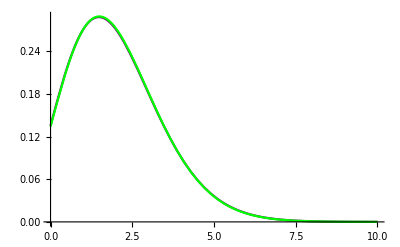

```mathematica
Plot[{poison[x],binomial[x]},{x,0,10}, PlotStyle->{{Purple},{Green}}]
```